```mathematica
Plot[x^2, {x,0,2},
Filling->Axis,
AxesLabel->{x,f(x)},
LabelStyle->{FontSize->15}]
```

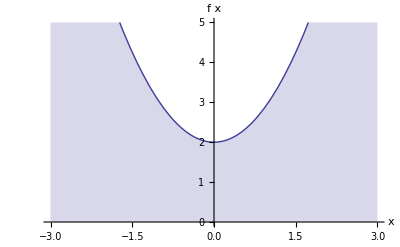

```mathematica
one=Plot[x^2 +2, {x,-3,3},
PlotRange->{0,5},
Filling->Axis,
AxesLabel->{x,f(x)},
LabelStyle->{FontSize->15}]
```

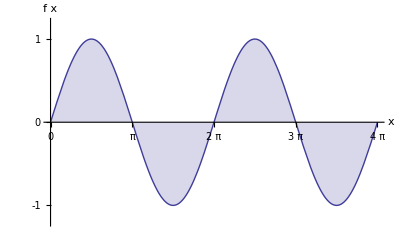

```mathematica
two=Plot[Sin[x], {x,0,4Pi},
PlotRange->{-1.2,1.2},
Filling->Axis,
AxesLabel->{x,f(x)},
LabelStyle->{FontSize->15},
Ticks ->{{0,Pi,2Pi,3Pi,4Pi},{-1,0,1}}]
```

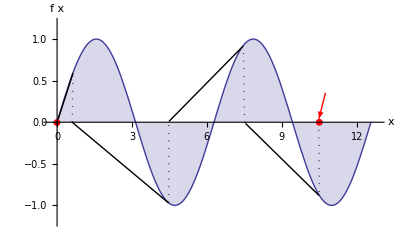

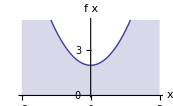
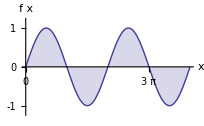
GraphicsGrid[{-Graphics-},{-Graphics-}]

```mathematica
GraphicsGrid[{one},{two}]
```